14.1942

2.27108

7.09712

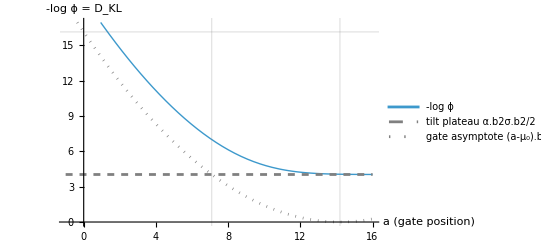

```mathematica
(*---parameters---*)
σ=2.5;
L0=10^7.;
ζ=0.5;
μ0=σ Sqrt[2 Log[L0]]     (*naïve peak;EVT edge sits at a=0*)
β=Sqrt[2 Log[L0]]/σ     (*entropy slope β**)
α=ζ β;                    (*one round of EP*)
μ1=μ0-α σ^2             (*tilted mean*)

(*---building blocks---*)
nd=NormalDistribution[0,1];
ρ[x_]:=PDF[nd,x]/CDF[nd,x];          (*inverse Mills ratio*)
w[a_]:=(a-μ1)/σ;
mlogϕ[a_]:=α^2 σ^2/2+α σ ρ[w[a]]-Log[CDF[nd,w[a]]];

(*---two limiting references---*)
tiltPlateau=α^2 σ^2/2;                  (*slack-gate limit*)
gateAsymp[a_]:=(a-μ0)^2/(2 σ^2);      (*deep-cut limit,valid for a<μ0*)

(*---plot---*)
Plot[{mlogϕ[a],tiltPlateau,gateAsymp[a]},{a,-1,16},PlotStyle->{Thick,{Dashed,Gray},{Dotted,Gray}},PlotRange->{0,1.05 Log[L0]},AxesLabel->{"a  (gate position)","-log ϕ = D_KL"},GridLines->{{0,μ1,μ0},{Log[L0]}},PlotLegends->{"-log ϕ","tilt plateau α.b2σ.b2/2","gate asymptote (a-μ₀).b2/2σ.b2"}]
```

1.15

1.51158×10^7

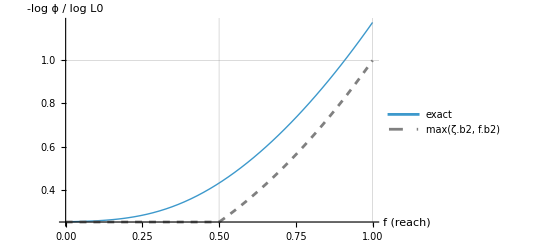

```mathematica
(*from data*)ζ=0.5;β=2.3;σ=2.5;          (*β*,σ measured/assumed*)
α=ζ β
L0=Exp[β^2 σ^2/2]                 (*ln L0=.bd β*.b2 σ.b2*)
μ0=β σ^2;
μ1=μ0-α σ^2;

nd=NormalDistribution[0,1];
ρ[x_]:=PDF[nd,x]/CDF[nd,x];
(*cost as a function of fractional reach f,in units of ln L0*)
s=β σ;                              (* =Sqrt[2 Log L0]*)
mlogϕN[f_]:=(α^2 σ^2/2+α σ ρ[(ζ-f) s]-Log[CDF[nd,(ζ-f) s]])/(β^2 σ^2/2);

Plot[{mlogϕN[f],Max[ζ^2,f^2]},{f,0,1},PlotStyle->{Thick,{Dashed,Gray}},GridLines->{{ζ,1},{ζ^2,1}},AxesLabel->{"f  (reach)","-log ϕ / log L0"},PlotLegends->{"exact","max(ζ.b2, f.b2)"}]
```

14.375

16.5312

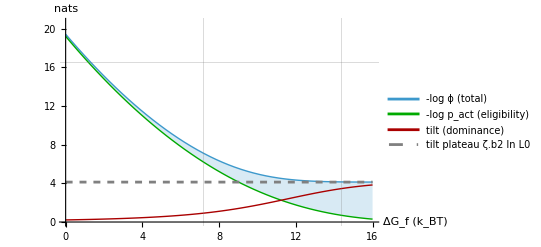

```mathematica
(*---parameters from data/heuristic pin---*)
ζ=0.5;β=2.3;σ=2.5;        (*σ from ln L0=.bd β*.b2 σ.b2≈16.5*)
α=ζ β;
μ0=β σ^2                           (*naïve peak;EVT edge at a=0*)
μ1=μ0-α σ^2;                       (*tilted mean (w=0 crossover)*)
lnL0=β^2 σ^2/2

(*---building blocks---*)
nd=NormalDistribution[0,1];
ρ[x_]:=PDF[nd,x]/CDF[nd,x];
w[a_]:=(a-μ1)/σ;
zp[a_]:=(a-μ0)/σ;

(*full cost (dominance) and gate-only cost (eligibility)*)
mlogϕ[a_]:=α^2 σ^2/2+α σ ρ[w[a]]-Log[CDF[nd,w[a]]];
gateKL[a_]:=-Log[CDF[nd,zp[a]]];     (* =-log p_act,exact*)
tiltKL[a_]:=α^2 σ^2/2+α σ ρ[w[a]]-Log[CDF[nd,w[a]]/CDF[nd,zp[a]]];

Plot[{mlogϕ[y],gateKL[y], tiltKL[y],α^2 σ^2/2},{y,0,16},PlotStyle->{Thick,{Thick,Darker@Green},{Thick,Darker@Red},{Dashed,Gray}},Filling->{1->{2}},(*shaded gap=tilt term*)PlotRange->{0,1.25 lnL0},AxesLabel->{"ΔG_f  (k_BT)","nats"},GridLines->{{0,μ1,μ0},{lnL0}},PlotLegends->{"-log ϕ (total) ","-log p_act (eligibility)","tilt (dominance)", "tilt plateau ζ.b2 ln L0"}]
```

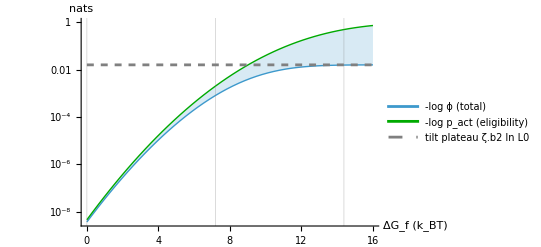

```mathematica
LogPlot[{Exp[-mlogϕ[y]],Exp[-gateKL[y]],Exp[-α^2 σ^2/2]},{y,0,16},PlotStyle->{Thick,{Thick,Darker@Green},{Dashed,Gray}},Filling->{1->{2}},(*shaded gap=tilt term*)PlotRange->Automatic,AxesLabel->{"ΔG_f  (k_BT)","nats"},GridLines->{{0,μ1,μ0},{lnL0}},PlotLegends->{"-log ϕ (total) ","-log p_act (eligibility)", "tilt plateau ζ.b2 ln L0"}]
```